```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}"}];
```

```mathematica
HsbUMP[λ_,t_,U_]=({{-(2 t^2 λ)/U, 0, 0, (2 t^2 λ)/U}, {0, U-(2 t^2 λ)/U, (2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U}, {0, (2 t^2 λ)/U, U-(2 t^2 λ)/U, -(2 t √(-4 t^2+U^2) λ)/U}, {(2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U, -(2 t √(-4 t^2+U^2) λ)/U, -2 U (-1+λ)+(6 t^2 λ)/U}});
HRMP[λ_,t_,U_]=({{-2 t+U-(U λ)/2, 0, 0, (U λ)/2}, {0, U-(U λ)/2, (U λ)/2, 0}, {0, (U λ)/2, U-(U λ)/2, 0}, {(U λ)/2, 0, 0, 2 t+U-(U λ)/2}});
HsbRMP[λ_,t_,U_]=({{-U (-2+λ)+(2 t^2 λ)/U, 0, 0, (2 t^2 λ)/U}, {0, U+(2 t^2 λ)/U-U λ, (2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U}, {0, (2 t^2 λ)/U, U+(2 t^2 λ)/U-U λ, (2 t √(-4 t^2+U^2) λ)/U}, {(2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U, (2 t √(-4 t^2+U^2) λ)/U, -(6 t^2 λ)/U+U λ}});
```

```mathematica
ϵsbUMP[U_,t_,λ_]=Eigenvalues[HsbUMP[λ,t,U]];
ϵsbRMP[U_,t_,λ_]=Eigenvalues[HsbRMP[λ,t,U]];
```

```mathematica
Show[
{Plot3D[Evaluate[Re[ϵsbUMP[7,1,rλ+ⅈ zλ]]],{rλ,-0,1.5},{zλ,0,1},PlotStyle->Opacity[0.7],BoxRatios->{1, 1, 1},
ImageSize->Large,MaxRecursion->6,Mesh->5,Boxed->False,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},
AxesLabel->{
MaTeX["\\text{Re}(\\lambda)",Magnification->1.5],
MaTeX["\\text{Im}(\\lambda)",Magnification->1.5],
Rotate[MaTeX["\\text{Re}(E_\\text{UMP})/t",Magnification->1.5],π/2]},
AxesStyle->Directive[Thick,18,Black]
],
Graphics3D[{Opacity[0.5],Cylinder[{{0,0,-4},{0,0,20}},1]}]},PlotRange->{{0,1.2},{0,1.2},{-2.4,17}},Boxed->False
]
```

-Graphics3D-

```mathematica
Show[
{Plot3D[Evaluate[Re[ϵsbRMP[7,1,rλ+ⅈ zλ]]],{rλ,-0,1.5},{zλ,0,1},PlotStyle->Opacity[0.7],BoxRatios->{1, 1, 1},
ImageSize->Large,MaxRecursion->6,Mesh->5,Boxed->False,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},
AxesLabel->{
MaTeX["\\text{Re}(\\lambda)",Magnification->1.5],
MaTeX["\\text{Im}(\\lambda)",Magnification->1.5],
Rotate[MaTeX["\\text{Re}(E_\\text{RMP})/t",Magnification->1.5],π/2]},
AxesStyle->Directive[Thick,18,Black]
],
Graphics3D[{Opacity[0.5],Cylinder[{{0,0,-4},{0,0,20}},1]}]},PlotRange->{{0,1.2},{0,1.2},{-2.4,17}},Boxed->False
]
```

-Graphics3D-

```mathematica
Solve[
{
Det[HRMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]],D[Det[HRMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]], Ε]
}==0,{Ε,λ}]
```

{{Ε→ⅈ (2 t-ⅈ U),λ→-(4 ⅈ t)/U},{Ε→-ⅈ (2 t+ⅈ U),λ→(4 ⅈ t)/U},{Ε→U,λ→0}}

```mathematica
RsbUMP[t_,U_]:=
Sort[
Abs[λ]/.NSolve[
{
Det[HsbUMP[λ,t,U]-Ε IdentityMatrix[Length[HsbUMP[λ,t,U]]]],D[Det[HsbUMP[λ,t,U]-Ε IdentityMatrix[Length[HsbUMP[λ,t,U]]]], Ε]
}==0,{Ε,λ},WorkingPrecision->30]
]//DeleteDuplicates
```

```mathematica
RsbRMP[t_,U_]:=
Sort[
Abs[λ]/.NSolve[
{
Det[HsbRMP[λ,t,U]-Ε IdentityMatrix[Length[HsbRMP[λ,t,U]]]],D[Det[HsbRMP[λ,t,U]-Ε IdentityMatrix[Length[HsbRMP[λ,t,U]]]], Ε]
}==0,{Ε,λ}]
]//DeleteDuplicates
```

```mathematica
RsbUMP[1,3.]
```

{0,0.59615273075470236756143690263,1.069167393537735451985283867,4.7360418071690241675091349177,253096.68257062381809477900752,253098.38257673314352786791889,8.0063993375475441337622650107×10^16}

```mathematica
TabRsbUMP=With[{ΔU=1/100},Table[{U,RsbUMP[1,U]},{U,2+ΔU,10,ΔU}]];
TabRsbRMP=With[{ΔU=1/100},Table[{U,RsbRMP[1,U]},{U,2+ΔU,10,ΔU}]];
```

$Aborted

$Aborted

```mathematica
TabRRMP=With[{ΔU=1/100},Table[{U,4/U},{U,ΔU,10,ΔU}]];
```

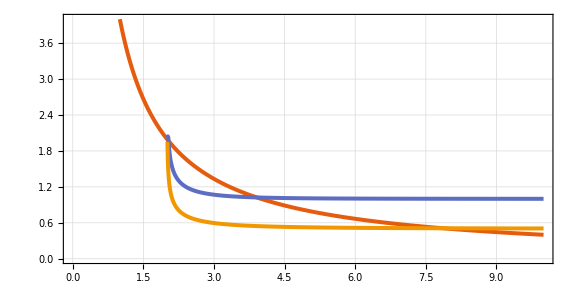

```mathematica
ListPlot[{
TabRadConvRMP,
Table[{TabRsbUMP⟦k,1⟧,TabRsbUMP⟦k,2,3⟧},{k,Length[TabRsbUMP]}],
Table[{TabRsbUMP⟦k,1⟧,TabRsbUMP⟦k,2,2⟧},{k,Length[TabRsbUMP]}]
},Joined->True,InterpolationOrder->1,PlotTheme->"Scientific",
PlotRange->{{0,10},{0,4}},PlotStyle->Thickness[0.005],
AspectRatio->1/2,
BaseStyle->20,ImageSize->Large,GridLines->Automatic,FrameLabel->{MaTeX["U/t",FontSize->20],MaTeX["\\text{Radius of convergence } r_c",FontSize->20]},
PlotLegends->Placed[{MaTeX["r_c \\text{ for RMP ground state}",FontSize->20],MaTeX["r_c \\text{ for UMP ground state}",FontSize->20],MaTeX["r_c \\text{ for UMP excited state}",FontSize->20]},{Right,Top}]]
```